```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/brianturnquist/Documents/BoonLogic/repos/boon-docs/docs/Amber101/SensorFusionExample

```mathematica
DataFileNames=FileNames["*.xlsx"]
```

{cavitation 1760 RPM.xlsx,high shaft misalignment1760 RPM.xlsx,low shaft misalignment 1760 RPM.xlsx,med shaft misalignment1760 RPM.xlsx,Normal run 1760 RPM 12-11-2020.xlsx,not running.xlsx}

```mathematica
FileExistsQ/@DataFileNames
```

{True,True,True,True,True,True}

```mathematica
ReadAMIDataFile[FilePath_]:=Module[{TheData,HeaderRow,IndexesExcluded,ColumnsExcluded,IndexesIncluded},
Print["Processing file: ", FilePath];
TheData=Import[FilePath]⟦1⟧;
{HeaderRow,TheData}=TakeDrop[TheData,1];
HeaderRow=HeaderRow⟦1⟧;
IndexesExcluded={1};
ColumnsExcluded=HeaderRow⟦IndexesExcluded⟧;
Print["Dropping column(s): "<>ToString[ColumnsExcluded]];
IndexesIncluded=Complement[Range[Length[HeaderRow]],IndexesExcluded];
HeaderRow=HeaderRow⟦IndexesIncluded⟧;
Print["Keeping column(s): "<>ToString[HeaderRow]];
TheData=Transpose[TheData]⟦IndexesIncluded⟧;
Return[TheData];
]
```

## Import and Preprocess

```mathematica
Cavitation=ReadAMIDataFile[DataFileNames⟦1⟧];
HighShaftMisalignment=ReadAMIDataFile[DataFileNames⟦2⟧];
LowShaftMisalignment=ReadAMIDataFile[DataFileNames⟦3⟧];
MedShaftMisalignment=ReadAMIDataFile[DataFileNames⟦4⟧];
NormalData=ReadAMIDataFile[DataFileNames⟦5⟧];
NotRunning=ReadAMIDataFile[DataFileNames⟦6⟧];
```

Processing file: cavitation 1760 RPM.xlsx

Dropping column(s): {PCTimeStamp}

Keeping column(s): {Temperature, Vin, RotVelocity, XRMS, YRMS, ZRMS, XFFTOutBins1, XFFTOutBins2, XFFTOutBins3, XFFTOutBins4, XFFTOutBins5, YFFTOutBins1, YFFTOutBins2, YFFTOutBins3, YFFTOutBins4, YFFTOutBins5, ZFFTOutBins1, ZFFTOutBins2, ZFFTOutBins3, ZFFTOutBins4, ZFFTOutBins5}

Processing file: high shaft misalignment1760 RPM.xlsx

Dropping column(s): {PCTimeStamp}

Keeping column(s): {Temperature, Vin, RotVelocity, XRMS, YRMS, ZRMS, XFFTOutBins1, XFFTOutBins2, XFFTOutBins3, XFFTOutBins4, XFFTOutBins5, YFFTOutBins1, YFFTOutBins2, YFFTOutBins3, YFFTOutBins4, YFFTOutBins5, ZFFTOutBins1, ZFFTOutBins2, ZFFTOutBins3, ZFFTOutBins4, ZFFTOutBins5}

Processing file: low shaft misalignment 1760 RPM.xlsx

Dropping column(s): {PCTimeStamp}

Keeping column(s): {Temperature, Vin, RotVelocity, XRMS, YRMS, ZRMS, XFFTOutBins1, XFFTOutBins2, XFFTOutBins3, XFFTOutBins4, XFFTOutBins5, YFFTOutBins1, YFFTOutBins2, YFFTOutBins3, YFFTOutBins4, YFFTOutBins5, ZFFTOutBins1, ZFFTOutBins2, ZFFTOutBins3, ZFFTOutBins4, ZFFTOutBins5}

Processing file: med shaft misalignment1760 RPM.xlsx

Dropping column(s): {PCTimeStamp}

Keeping column(s): {Temperature, Vin, RotVelocity, XRMS, YRMS, ZRMS, XFFTOutBins1, XFFTOutBins2, XFFTOutBins3, XFFTOutBins4, XFFTOutBins5, YFFTOutBins1, YFFTOutBins2, YFFTOutBins3, YFFTOutBins4, YFFTOutBins5, ZFFTOutBins1, ZFFTOutBins2, ZFFTOutBins3, ZFFTOutBins4, ZFFTOutBins5}

Processing file: Normal run 1760 RPM 12-11-2020.xlsx

Dropping column(s): {PCTimeStamp}

Keeping column(s): {Temperature, Vin, RotVelocity, XRMS, YRMS, ZRMS, XFFTOutBins1, XFFTOutBins2, XFFTOutBins3, XFFTOutBins4, XFFTOutBins5, YFFTOutBins1, YFFTOutBins2, YFFTOutBins3, YFFTOutBins4, YFFTOutBins5, ZFFTOutBins1, ZFFTOutBins2, ZFFTOutBins3, ZFFTOutBins4, ZFFTOutBins5}

Processing file: not running.xlsx

Dropping column(s): {PCTimeStamp}

Keeping column(s): {Temperature, Vin, RotVelocity, XRMS, YRMS, ZRMS, XFFTOutBins1, XFFTOutBins2, XFFTOutBins3, XFFTOutBins4, XFFTOutBins5, YFFTOutBins1, YFFTOutBins2, YFFTOutBins3, YFFTOutBins4, YFFTOutBins5, ZFFTOutBins1, ZFFTOutBins2, ZFFTOutBins3, ZFFTOutBins4, ZFFTOutBins5}

```mathematica
NormalizeXYZ[DataSet_]:=Join[Take[DataSet,{1,6}],Table[Sqrt[Total[DataSet⟦{7,12,17}+i⟧^2]],{i,0,4}]]
```

```mathematica
NormalData=Transpose[NormalizeXYZ[NormalData]];
HighShaftMisalignment=Transpose[NormalizeXYZ[HighShaftMisalignment]];
Cavitation=Transpose[NormalizeXYZ[Cavitation]];
LowShaftMisalignment=Transpose[NormalizeXYZ[LowShaftMisalignment]];
MedShaftMisalignment=Transpose[NormalizeXYZ[MedShaftMisalignment]];
NotRunning=Transpose[NormalizeXYZ[NotRunning]];
Dimensions/@{NormalData,HighShaftMisalignment,Cavitation,LowShaftMisalignment,MedShaftMisalignment,NotRunning}
```

{{20197,11},{18,11},{28,11},{18,11},{18,11},{13,11}}

```mathematica
NormalizedHeader={"Temperature", "Vin", "RotVelocity", "XRMS", "YRMS", "ZRMS", "FreqBin1", "FreqBin2", "FreqBin3", "FreqBin4", "FreqBin5"};
```

```mathematica
ColsToKeep={7,8,9,10,11};
NormalizedHeader=NormalizedHeader⟦ColsToKeep⟧
NormalData=#⟦ColsToKeep⟧&/@NormalData;
HighShaftMisalignment=#⟦ColsToKeep⟧&/@HighShaftMisalignment;
Cavitation=#⟦ColsToKeep⟧&/@Cavitation⟦ColsToKeep⟧;
LowShaftMisalignment=#⟦ColsToKeep⟧&/@LowShaftMisalignment;
MedShaftMisalignment=#⟦ColsToKeep⟧&/@MedShaftMisalignment;
NotRunning=#⟦ColsToKeep⟧&/@NotRunning;
Dimensions/@{NormalData,HighShaftMisalignment,Cavitation,LowShaftMisalignment,MedShaftMisalignment,NotRunning}
```

{FreqBin1,FreqBin2,FreqBin3,FreqBin4,FreqBin5}

{{20197,5},{18,5},{5,5},{18,5},{18,5},{13,5}}

## Generate Data

```mathematica
ModNormalData={#⟦1⟧,#⟦2⟧,#⟦3⟧,(#⟦1⟧+#⟦5⟧)/2,#⟦5⟧}&/@NormalData;
```

```mathematica
MinMaxFeature4=MinMax[Transpose[ModNormalData]⟦4⟧]
```

{0.0181996,0.0479053}

```mathematica
RelationalAnomaly1=Take[{#⟦1⟧,#⟦2⟧,#⟦3⟧,RandomReal[{0.02,0.035}],#⟦5⟧}&/@ModNormalData,-50];
```

```mathematica
(*RelationalAnomaly2=Take[{#⟦1⟧,#⟦2⟧,#⟦3⟧,Max[{0.01,(#⟦1⟧-#⟦5⟧)/2}],#⟦5⟧}&/@NormalData,-50];*)
```

```mathematica
RelationalAnomaly2=Take[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧*0.75,#⟦5⟧}&/@ModNormalData,-20];
```

```mathematica
(* Start with machine off *)
FullDataSet=RandomChoice[ModNormalData,1000];

(* Now add in the normal run data *)
GroundTruthVals={Length[FullDataSet]};
FullDataSet=Join[FullDataSet,ModNormalData];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,5000]];
EndOfTrainingData=Length[FullDataSet]
Print["End of Training Data at "<>ToString[EndOfTrainingData]];

(* Add some normal data after the training set *)
AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=RandomChoice[ModNormalData,1000];
AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,5000]];

(* Start anomalies here separated by normal data *)
AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,RelationalAnomaly1];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,5000]];

AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,RelationalAnomaly2];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,1000]];

AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,LowShaftMisalignment];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,1000]];

AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,RandomChoice[NotRunning,1000]];

AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,MedShaftMisalignment];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,1000]];

AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,HighShaftMisalignment];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,1000]];

AppendTo[GroundTruthVals,Length[FullDataSet]];
FullDataSet=Join[FullDataSet,Cavitation];
FullDataSet=Join[FullDataSet,RandomChoice[ModNormalData,2000]];

Dimensions[FullDataSet]
Print[GroundTruthVals]
```

26197

End of Training Data at 26197

{18129,5}

{1000,26197,1000,6000,11050,12070,13088,14088,15106,16124}

```mathematica
Export["AmberDemoDataSet.csv",FullDataSet]
```

AmberDemoDataSet.csv

```mathematica
Export["AmberDemoDataSet.gnd",GroundTruthVals,"CSV"]
```

AmberDemoDataSet.gnd

## Nano Setup

```mathematica
<<NanoREST`
```

```mathematica
nano=OpenNano["nano"]
```

<|api-key→no-key,api-tenant→no-tenant,url→http://localhost:5007/expert/v3/,instance→nano|>

## Nano Run

```mathematica
NumFeatures = Length[ModNormalData⟦1⟧]
```

5

```mathematica
ConfigureNano[nano,"float32",NumFeatures,AutotuneByFeature->True]
GetConfig[nano]
```

<|clusterMode→batch,numericFormat→float32,features→{<|minVal→0,maxVal→10,weight→1|>,<|minVal→0,maxVal→10,weight→1|>,<|minVal→0,maxVal→10,weight→1|>,<|minVal→0,maxVal→10,weight→1|>,<|minVal→0,maxVal→10,weight→1|>},percentVariation→0.05,accuracy→0.99,streamingWindowSize→1,autoTuning→<|autoTuneByFeature→True,autoTunePV→True,autoTuneRange→True,maxClusters→1000,exclusions→{}|>|>

```mathematica
(* Load the training set*)
```

```mathematica
LoadData[nano,Take[FullDataSet,EndOfTrainingData]]
GetBufferStatus[nano]["totalBytesWritten"]/(NumFeatures*4)
```

26197

```mathematica
(* Tune the nano *)
```

```mathematica
SetLearningStatus[nano,True]
AutotuneConfig[nano]
GetConfig[nano]
```

<|clusterMode→batch,numericFormat→float32,features→{<|minVal→0.0321524,maxVal→0.0340845,weight→1|>,<|minVal→0.00176497,maxVal→0.00561906,weight→1|>,<|minVal→0.00189566,maxVal→0.00990508,weight→1|>,<|minVal→0.0246437,maxVal→0.0400628,weight→1|>,<|minVal→0.0168638,maxVal→0.0470189,weight→1|>},percentVariation→0.129,accuracy→0.99,streamingWindowSize→1,autoTuning→<|autoTuneByFeature→True,autoTunePV→True,autoTuneRange→True,maxClusters→1000,exclusions→{}|>|>

```mathematica
RunNano[nano]
SetLearningStatus[nano,False]
```

```mathematica
CG=Transpose[{GetNanoStatus[nano]["clusterGrowth"],Range[Length[GetNanoStatus[nano]["clusterGrowth"]]]-1}]
```

{{0,0},{1,1},{4,2},{5,3},{6,4},{9,5},{10,6},{12,7},{22,8},{23,9},{25,10},{34,11},{35,12},{50,13},{55,14},{59,15},{60,16},{63,17},{97,18},{119,19},{122,20},{149,21},{153,22},{161,23},{186,24},{213,25},{242,26},{254,27},{260,28},{336,29},{347,30},{350,31},{378,32},{388,33},{461,34},{476,35},{477,36},{508,37},{597,38},{610,39},{694,40},{869,41},{883,42},{1007,43},{1028,44},{1029,45},{1042,46},{1145,47},{1291,48},{1361,49},{1707,50},{1817,51},{1821,52},{2524,53},{3213,54},{3241,55},{4404,56},{5258,57},{5652,58},{6125,59},{6542,60},{6821,61},{7342,62},{10329,63},{12346,64},{13958,65},{13962,66},{14370,67},{17188,68},{17905,69},{18983,70},{19306,71},{20814,72}}

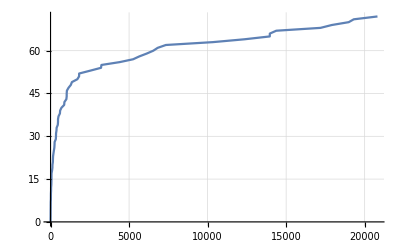

```mathematica
ListLinePlot[CG,GridLines->Automatic]
```

```mathematica
LoadData[nano,FullDataSet]
RunNano[nano]
GetBufferStatus[nano]
```

<|totalBytesWritten→866520,totalBytesProcessed→866520,totalBytesInBuffer→866520|>

```mathematica
AllResults=GetNanoResults[nano,Results->All];
```

```mathematica
Keys[AllResults]
```

{ID,SI,RI,FI,DI}

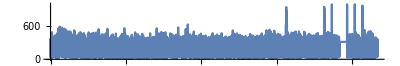

```mathematica
ListLinePlot[AllResults["SI"],PlotRange->All,AspectRatio->1/6, ImageSize->Full]
```

```mathematica
TrFullDataSet=Transpose[FullDataSet];
```

```mathematica
ListLinePlot[TrFullDataSet,PlotRange->All,ImageSize->Full,GridLines->Automatic,AspectRatio->1/6]
```

-Graphics-

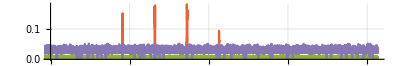

```mathematica
ListLinePlot[TrFullDataSet,PlotRange->{{25000,All},All},ImageSize->Full,GridLines->Automatic,AspectRatio->1/6]
```

```mathematica
Manipulate[ListLinePlot[FullDataSet⟦i⟧,PlotRange->{0,.05},PlotMarkers->Automatic],{i,1,Length[FullDataSet],1}]
```

Part::partd: Part specification FullDataSet⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: FullDataSet⟦1⟧ is not a list of numbers or pairs of numbers.

## Import from Amber

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/brianturnquist/Documents/BoonLogic/repos/boon-docs/docs/Amber101/SensorFusionExample

```mathematica
DemoData=Transpose[Import["AmberDemo_Data.csv"]];
```

```mathematica
Dimensions[DemoData]
```

{5,49495}

```mathematica
DemoDataPlots=ListLinePlot[#,PlotRange->All,ImageSize->Full,GridLines->Automatic,AspectRatio->1/6]&/@DemoData;
```

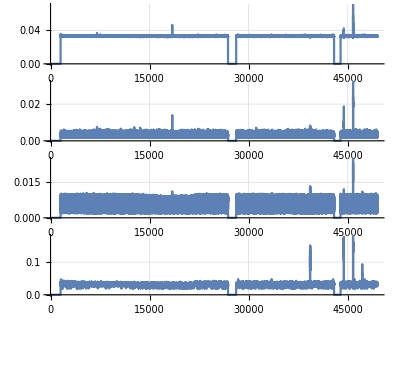

```mathematica
GraphicsColumn[DemoDataPlots]
```

```mathematica
AmberResults=Transpose[Drop[Import["AmberDemo_Results.csv"],1]];
```

```mathematica
AmberResultsPlots=ListLinePlot[#,PlotRange->All,GridLines->Automatic,AspectRatio->1/6]&/@AmberResults;
```

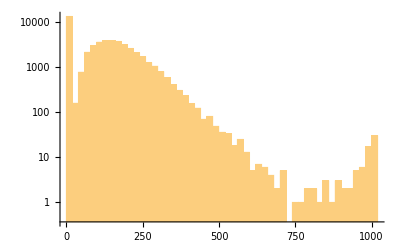

```mathematica
Histogram[AmberResults⟦2⟧,ScalingFunctions->{Automatic,"Log"},PlotRange->All]
```

```mathematica
s
```

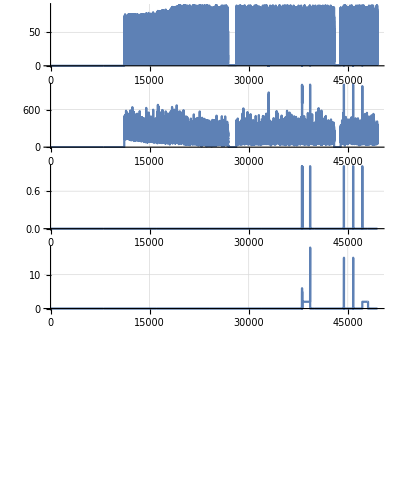

```mathematica
GraphicsColumn[AmberResultsPlots,ImageSize->Full]
```